```mathematica
GroundState[mat_?HermitianMatrixQ]:=Module[{gr,u,e,m,len,pos},
e=Eigenvalues[mat];
m=Min[e];
pos=Position[e,m]//Flatten;
u=Eigenvectors[mat];
gr=Mean[Table[Outer[Times,u[[i]],u[[i]]],{i,pos}]];
Return[gr]
]


gts::warn="to avoid overflow  for  temparature `1`  ground state is calculated instead .";
ThermalState[rho_,t_,chop_:10^-8]/;If[Chop[t,chop]≠ 0,True,Message[gts::warn,t];True]:=Module[{ther},
ther=If[Chop[t,chop]==0,GroundState[rho],MatrixExp[- rho/t]/Tr[MatrixExp[- rho/t]]];
Return[ther]
]
(*not ≠ in if massage while it is = inside if function *)
```

```mathematica
HeisenbergXYZ[jx_,jy_,jz_,dz_]:=jx*KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]+
jy*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+
jz*KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]+
dz*KroneckerProduct[PauliMatrix[1],PauliMatrix[2]]-
dz*KroneckerProduct[PauliMatrix[2],PauliMatrix[1]]
```

```mathematica
localFisher[jx_,jy_,jz_,dz_,t_]:=Block[{λ,W},

λ=Eigenvalues[ThermalState[HeisenbergXYZ[jx,jy,jz,dz],t]//N];
W[i_,j_]:=Sum[(1-KroneckerDelta[m,n])*(2λ[[m]]*λ[[n]])/(λ[[m]]+λ[[n]])KMatrix[i][[m,n]]*KMatrix[j][[n,m]],{n,4},{m,4}];
Return[1-Max[Table[W[i,i],{i,3}]]]]
```

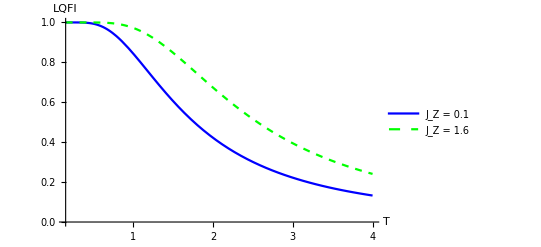

```mathematica
Plot[{localFisher[-1,-.5,.1,1,t],localFisher[-1,-.5,1.6,1,t]},{t,.15,4},PlotStyle->{{Blue},{Green,Dashed}},PlotLegends->{"J_Z = 0.1","J_Z = 1.6"},AxesLabel->{Style["T",Black,FontSize->15],Style["LQFI",Black,FontSize->15]}]
```

```mathematica
{
```